```mathematica
SetDirectory["/Users/tobiastiecke/Documents/Math/ABM/Na23K40/"];
```

## General

### Initialization

```mathematica
Off[ClebschGordan::"phy"]
Off[General::"spell1"]
Off[General::"spell"]
<<"ErrorBarPlots`";<<"PlotLegends`"
```

### Constants

```mathematica
IILi6=1;
IILi7=3/2;
IINa23=3/2;         
IIK39=3/2;
IIK40=4;
IIK41=3/2;
IIRb85=5/2;
IIRb87=3/2;
IICs133=7/2;
```

```mathematica
SSLi6=1/2;
SSLi7=1/2;
SSNa23=1/2;
SSK39=1/2;
SSK40=1/2;
SSK41=1/2;
SSRb85=1/2;
SSRb87=1/2;
SSCs133=1/2;
```

```mathematica
AhfLi6=152.1368407*10^6;               (*arimondo*)
AhfLi7=401.7520433*10^6;               (*arimondo*)
AhfNa23=885.8130644*10^6;               (*arimondo*)
AhfK39=230.859860*10^6;               (*arimondo*)
AhfK40=-285.7308*10^6;               (*arimondo*)
AhfK41=127.0069352*10^6;               (*arimondo*)
AhfRb85=1011.910813*10^6;   (*arimondo*)
AhfRb87=3417.34130642*10^6;   (*arimondo*)
AhfCs133=2298.1579425*10^6;   (*arimondo*)
```

```mathematica
gS=2.0023193043622;                   (*NIST site*)
gILi6=-0.0004476540;               (*arimondo*)
gILi7=-0.0011822130;               (*arimondo*)
gINa23=-0.0008046108;               (*arimondo*)
gIK39=-0.00014193489;               (*arimondo*)
gIK40=+0.000176490;               (*arimondo*)
gIK41=-0.00007790600;               (*arimondo*)
gIRb85=-0.0002936400;          (*arimondo*)
gIRb87=-0.0009951414;          (*arimondo*)
gICs133=-0.00039885395;          (*arimondo*)
```

```mathematica
mLi6=6.0151223;                   (*NIST site*)
mLi7=7.0160040;                   (*NIST site*)
mNa23=22.98976967;                   (*NIST site*)
mK39=38.9637069;                   (*NIST site*)
mK40=39.96399867;                   (*NIST site*)
mK41=40.96182597;                   (*NIST site*)
mRb85=84.9117893;                   (*NIST site*)
mRb87=86.9091835;                   (*NIST site*)
mCs133=132.905447;                   (*NIST site*)
```

```mathematica
h=6.62606896*10^-34;                   (*NIST site*)
ℏ=h/(2π);
muB=9.27400915*10^-24;                   (*NIST site*)
a0SI=5.2917720859*10^-11;                   (*NIST site*)
a0=1;
hbar=1;
kB=1.3806504*10^-23;                   (*NIST site*)
me=9.10938215*10^-31;                   (*NIST site*)
u=1.660538782*10^-27;                   (*NIST site*)
```

```mathematica
C6Rb=4698 a0;                (* from Chris' thesis*)
C6LiK=2322 a0;            (*heternuclear C6 from Julienne/Tiesinga *)
(*C8LiK=192490;
C6LiNa=1459.4 a0;*)
Eh=4.35974394*10^-18;                   (*NIST site*)

(*THESE ARE THE PROPER (CHECKED) CONSTANTS!!! only if every constant is followed by a line which includes the reference*)
```

This variable is the stepsize (in Gauss) for which we calculate the molecular hyperfine states. For determining where the feshbach resonances are this value should be small (0.1G or so) however this makes the notebook slow and big, so for plotting use just use 3G or so.

```mathematica
deltaB=2.5;
minBPlot=0;
maxBPlot=1200;
highBLimit=1000;
```

## Choice of species

```mathematica
SS1=SSNa23;
SS2=SSK40;
II1=IINa23;
II2=IIK40;
Ahf1=AhfNa23;
Ahf2=AhfK40;
gI1=gINa23;
gI2=gIK40;
```

```mathematica
μ=(mNa23*mK40)/(mNa23+mK40)*u
```

2.42343×10^-26

```mathematica
maxTotalMF=SS1+SS2+II1+II2
```

13/2

## Free atom calculations

### Atom1

```mathematica
Ahf=Ahf1;
II=II1;
gI=gI1;
SS=SS1;
```

```mathematica
ISbasis=Flatten[Table[Table[{mI,mS},{mS,-SS,SS,1}],{mI,-II,II,1}],1]
```

{{-3/2,-1/2},{-3/2,1/2},{-1/2,-1/2},{-1/2,1/2},{1/2,-1/2},{1/2,1/2},{3/2,-1/2},{3/2,1/2}}

```mathematica
FmFbasis=Flatten[Table[{FF,mF},{FF,II-SS,II+SS},{mF,-FF,FF,1}],1]
```

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
nStatesF=Length[FmFbasis]
nStatesI=Length[ISbasis]
```

8

8

```mathematica
ClebschMatrix=Table[ClebschGordan[{II,ISbasis[[iIS,1]]},{SS,ISbasis[[iIS,2]]},{FmFbasis[[iFmF,1]],FmFbasis[[iFmF,2]]}],{iFmF,1,nStatesF},{iIS,1,nStatesI}];
```

ClebschGordan::phy: ThreeJSymbol[{3/2,-3/2},{1/2,-1/2},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2,-1/2},{1/2,1/2},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2,1/2},{1/2,-1/2},{1,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
couplingMatrixElement=Table[1/2(FF(FF+1)-II(II+1)-SS(SS+1))/.{FF->FmFbasis[[i,1]]},{i,nStatesF}];
```

```mathematica
HyperfineH=Table[h*Ahf*(ClebschMatrix[[All,i]]*ClebschMatrix[[All,j]]).couplingMatrixElement,{i,nStatesI},{j,nStatesI}];
```

```mathematica
ZeemanH=Table[KroneckerDelta[i,j]*muB*B*10^-4*(gS*ISbasis[[i,2]]+gI*ISbasis[[i,1]]),{i,1,nStatesI},{j,1,nStatesI}];
```

```mathematica
TotalH=HyperfineH+ZeemanH;
```

```mathematica
TotalHAtom1=TotalH;
```

```mathematica
Energy=10^-6/h Eigenvalues[TotalH];
```

```mathematica
nStatesAtom1=Length[Energy];
```

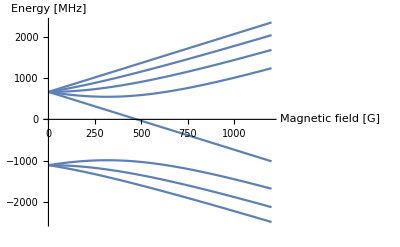

```mathematica
tmpPl=Table[0,{i,nStatesAtom1}];
For[i=1,i<=nStatesAtom1,
tmpPl[[i]]=Plot[Energy[[i]],{B,minBPlot,maxBPlot},AxesLabel->{"Magnetic field [G]","Energy [MHz]"},DisplayFunction->Identity];
i=i+1];
Show[tmpPl,DisplayFunction->$DisplayFunction,PlotRange->All]
```

```mathematica
Sort[Transpose[Eigensystem[TotalH/h/.B->maxBPlot]]]//MatrixForm
```

(-2.48211×10^9 | {0.,0.,0.,0.,0.,-0.172352,0.985035,0.}
-2.1226×10^9 | {0.,0.,0.,-0.239981,0.970778,0.,0.,0.}
-1.67759×10^9 | {0.,-0.273611,0.96184,0.,0.,0.,0.,0.}
-1.01511×10^9 | {1.,0.,0.,0.,0.,0.,0.,0.}
1.23739×10^9 | {0.,0.96184,0.273611,0.,0.,0.,0.,0.}
1.6797×10^9 | {0.,0.,0.,0.970778,0.239981,0.,0.,0.}
2.0365×10^9 | {0.,0.,0.,0.,0.,0.985035,0.172352,0.}
2.34383×10^9 | {0.,0.,0.,0.,0.,0.,0.,1.})

```mathematica
ISbasisAtom1=ISbasis
FmFbasisAtom1=FmFbasis
```

{{-3/2,-1/2},{-3/2,1/2},{-1/2,-1/2},{-1/2,1/2},{1/2,-1/2},{1/2,1/2},{3/2,-1/2},{3/2,1/2}}

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
EnergyAtom1=Energy;
```

```mathematica
EnergyAtom1//MatrixForm
```

(1.50919×10^27 (4.40209×10^-25-9.27357×10^-28 B)
1.50919×10^27 (4.40209×10^-25+9.27357×10^-28 B)
7.54595×10^26 (-2.93473×10^-25-√(1.37802×10^-48+3.45105×10^-54 B^2))
7.54595×10^26 (-2.93473×10^-25+√(1.37802×10^-48+3.45105×10^-54 B^2))
7.54595×10^26 (-2.93473×10^-25+1.49239×10^-30 B-√(1.37802×10^-48-2.18074×10^-51 B+3.45105×10^-54 B^2))
7.54595×10^26 (-2.93473×10^-25+1.49239×10^-30 B+√(1.37802×10^-48-2.18074×10^-51 B+3.45105×10^-54 B^2))
7.54595×10^26 (-2.93473×10^-25-1.49239×10^-30 B-√(1.37802×10^-48+2.18074×10^-51 B+3.45105×10^-54 B^2))
7.54595×10^26 (-2.93473×10^-25-1.49239×10^-30 B+√(1.37802×10^-48+2.18074×10^-51 B+3.45105×10^-54 B^2)))

### Atom2

```mathematica
Ahf=Ahf2;
II=II2;
gI=gI2;
SS=SS2;
```

```mathematica
ISbasis=Flatten[Table[Table[{mI,mS},{mS,-SS,SS,1}],{mI,-II,II,1}],1]
```

{{-4,-1/2},{-4,1/2},{-3,-1/2},{-3,1/2},{-2,-1/2},{-2,1/2},{-1,-1/2},{-1,1/2},{0,-1/2},{0,1/2},{1,-1/2},{1,1/2},{2,-1/2},{2,1/2},{3,-1/2},{3,1/2},{4,-1/2},{4,1/2}}

```mathematica
FmFbasis=Flatten[Table[{FF,mF},{FF,II-SS,II+SS},{mF,-FF,FF,1}],1]
```

{{7/2,-7/2},{7/2,-5/2},{7/2,-3/2},{7/2,-1/2},{7/2,1/2},{7/2,3/2},{7/2,5/2},{7/2,7/2},{9/2,-9/2},{9/2,-7/2},{9/2,-5/2},{9/2,-3/2},{9/2,-1/2},{9/2,1/2},{9/2,3/2},{9/2,5/2},{9/2,7/2},{9/2,9/2}}

```mathematica
nStatesF=Length[FmFbasis]
nStatesI=Length[ISbasis]
```

18

18

```mathematica
ClebschMatrix=Table[ClebschGordan[{II,ISbasis[[iIS,1]]},{SS,ISbasis[[iIS,2]]},{FmFbasis[[iFmF,1]],FmFbasis[[iFmF,2]]}],{iFmF,1,nStatesF},{iIS,1,nStatesI}];
```

ClebschGordan::phy: ThreeJSymbol[{4,-4},{1/2,-1/2},{7/2,7/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{4,-3},{1/2,1/2},{7/2,7/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{4,-2},{1/2,-1/2},{7/2,7/2}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
ClebschMatrix//MatrixForm
```

(0 | -(2 √2)/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(√7)/3 | (√2)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -√(2/3) | 1/(√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√5)/3 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/3 | (√5)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√3) | √(2/3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√2)/3 | (√7)/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | (2 √2)/3 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | (2 √2)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√2)/3 | (√7)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(√3) | √(2/3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | (√5)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√5)/3 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(2/3) | 1/(√3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√7)/3 | (√2)/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 √2)/3 | 1/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
couplingMatrixElement=Table[1/2(FF(FF+1)-II(II+1)-SS(SS+1))/.{FF->FmFbasis[[i,1]]},{i,nStatesF}];
```

```mathematica
HyperfineH=Table[h*Ahf*(ClebschMatrix[[All,i]]*ClebschMatrix[[All,j]]).couplingMatrixElement,{i,nStatesI},{j,nStatesI}];
```

```mathematica
ZeemanH=Table[KroneckerDelta[i,j]*muB*B*10^-4*(gS*ISbasis[[i,2]]+gI*ISbasis[[i,1]]),{i,1,nStatesI},{j,1,nStatesI}];
```

```mathematica
TotalH=HyperfineH+ZeemanH;
```

```mathematica
TotalHAtom2=TotalH;
```

```mathematica
Energy=10^-6/h Eigenvalues[TotalH];
```

```mathematica
nStatesAtom2=Length[Energy];
```

```mathematica
Energy
```

{1.50919×10^27 (-3.78654×10^-25-9.29131×10^-28 B),1.50919×10^27 (-3.78654×10^-25+9.29131×10^-28 B),7.54595×10^26 (9.46636×10^-26+8.18385×10^-31 B-√(7.25857×10^-49-1.7577×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26+8.18385×10^-31 B+√(7.25857×10^-49-1.7577×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26-8.18385×10^-31 B-√(7.25857×10^-49+1.7577×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26-8.18385×10^-31 B+√(7.25857×10^-49+1.7577×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26+1.63677×10^-31 B-√(7.25857×10^-49-3.51541×10^-52 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26+1.63677×10^-31 B+√(7.25857×10^-49-3.51541×10^-52 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26-1.63677×10^-31 B-√(7.25857×10^-49+3.51541×10^-52 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26-1.63677×10^-31 B+√(7.25857×10^-49+3.51541×10^-52 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26+1.14574×10^-30 B-√(7.25857×10^-49-2.46078×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26+1.14574×10^-30 B+√(7.25857×10^-49-2.46078×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26+4.91031×10^-31 B-√(7.25857×10^-49-1.05462×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26+4.91031×10^-31 B+√(7.25857×10^-49-1.05462×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26-4.91031×10^-31 B-√(7.25857×10^-49+1.05462×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26-4.91031×10^-31 B+√(7.25857×10^-49+1.05462×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26-1.14574×10^-30 B-√(7.25857×10^-49+2.46078×10^-51 B+3.44767×10^-54 B^2)),7.54595×10^26 (9.46636×10^-26-1.14574×10^-30 B+√(7.25857×10^-49+2.46078×10^-51 B+3.44767×10^-54 B^2))}

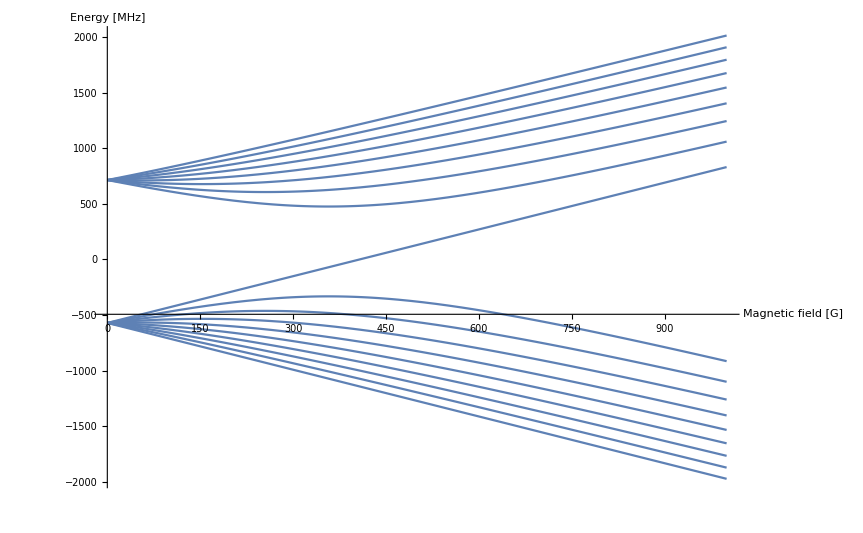

```mathematica
tmpPl=Table[0,{i,nStatesAtom2}];
For[i=1,i<=nStatesAtom2,
tmpPl[[i]]=Plot[Energy[[i]],{B,0,1000},AxesLabel->{"Magnetic field [G]","Energy [MHz]"},DisplayFunction->Identity];
i=i+1];
Show[tmpPl,DisplayFunction->$DisplayFunction,PlotRange->All]
```

```mathematica
Sort[Transpose[Eigensystem[TotalH/h/.B->maxBPlot]]]//MatrixForm
```

(-2.25414×10^9 | {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
-2.14809×10^9 | {0.,0.0914552,0.995809,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
-2.03674×10^9 | {0.,0.,0.,0.127875,0.99179,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
-1.9192×10^9 | {0.,0.,0.,0.,0.,0.15412,0.988052,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
-1.79431×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.173885,0.984766,0.,0.,0.,0.,0.,0.,0.,0.,0.}
-1.66048×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.187777,0.982212,0.,0.,0.,0.,0.,0.,0.}
-1.51546×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.194649,0.980873,0.,0.,0.,0.,0.}
-1.35584×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.190665,0.981655,0.,0.,0.}
-1.17605×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.164048,0.986452,0.}
1.11122×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}
1.32099×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.986452,-0.164048,0.}
1.50018×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.981655,-0.190665,0.,0.,0.}
1.65921×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.980873,-0.194649,0.,0.,0.,0.,0.}
1.80364×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.982212,-0.187777,0.,0.,0.,0.,0.,0.,0.}
1.93688×10^9 | {0.,0.,0.,0.,0.,0.,0.,0.984766,-0.173885,0.,0.,0.,0.,0.,0.,0.,0.,0.}
2.06118×10^9 | {0.,0.,0.,0.,0.,0.988052,-0.15412,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
2.17813×10^9 | {0.,0.,0.,0.99179,-0.127875,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
2.28888×10^9 | {0.,0.995809,-0.0914552,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.})

```mathematica
ISbasisAtom2=ISbasis
FmFbasisAtom2=FmFbasis
```

{{-4,-1/2},{-4,1/2},{-3,-1/2},{-3,1/2},{-2,-1/2},{-2,1/2},{-1,-1/2},{-1,1/2},{0,-1/2},{0,1/2},{1,-1/2},{1,1/2},{2,-1/2},{2,1/2},{3,-1/2},{3,1/2},{4,-1/2},{4,1/2}}

{{7/2,-7/2},{7/2,-5/2},{7/2,-3/2},{7/2,-1/2},{7/2,1/2},{7/2,3/2},{7/2,5/2},{7/2,7/2},{9/2,-9/2},{9/2,-7/2},{9/2,-5/2},{9/2,-3/2},{9/2,-1/2},{9/2,1/2},{9/2,3/2},{9/2,5/2},{9/2,7/2},{9/2,9/2}}

```mathematica
EnergyAtom2=Energy;
```

```mathematica
EnergyAtom2//MatrixForm
```

(1.50919×10^27 (-3.78654×10^-25-9.29131×10^-28 B)
1.50919×10^27 (-3.78654×10^-25+9.29131×10^-28 B)
7.54595×10^26 (9.46636×10^-26+8.18385×10^-31 B-√(7.25857×10^-49-1.7577×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26+8.18385×10^-31 B+√(7.25857×10^-49-1.7577×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26-8.18385×10^-31 B-√(7.25857×10^-49+1.7577×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26-8.18385×10^-31 B+√(7.25857×10^-49+1.7577×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26+1.63677×10^-31 B-√(7.25857×10^-49-3.51541×10^-52 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26+1.63677×10^-31 B+√(7.25857×10^-49-3.51541×10^-52 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26-1.63677×10^-31 B-√(7.25857×10^-49+3.51541×10^-52 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26-1.63677×10^-31 B+√(7.25857×10^-49+3.51541×10^-52 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26+1.14574×10^-30 B-√(7.25857×10^-49-2.46078×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26+1.14574×10^-30 B+√(7.25857×10^-49-2.46078×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26+4.91031×10^-31 B-√(7.25857×10^-49-1.05462×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26+4.91031×10^-31 B+√(7.25857×10^-49-1.05462×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26-4.91031×10^-31 B-√(7.25857×10^-49+1.05462×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26-4.91031×10^-31 B+√(7.25857×10^-49+1.05462×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26-1.14574×10^-30 B-√(7.25857×10^-49+2.46078×10^-51 B+3.44767×10^-54 B^2))
7.54595×10^26 (9.46636×10^-26-1.14574×10^-30 B+√(7.25857×10^-49+2.46078×10^-51 B+3.44767×10^-54 B^2)))

### sorted bases

#### Atom 1

```mathematica
highFieldEn=EnergyAtom1/.B->highBLimit
```

{-735.199,2063.92,-1879.69,1436.78,-1448.33,1007.68,-2220.45,1775.29}

```mathematica
sortedEns=Sort[highFieldEn]
```

{-2220.45,-1879.69,-1448.33,-735.199,1007.68,1436.78,1775.29,2063.92}

```mathematica
sEnergyAtom1={};
For[i=1,i≤nStatesAtom1,
pos=Flatten[Position[highFieldEn,sortedEns[[i]]]][[1]];
AppendTo[sEnergyAtom1,EnergyAtom1[[pos]]];
i++];
```

```mathematica
sFmFAtom1={{1,1},{1,0},{1,-1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}
```

{{1,1},{1,0},{1,-1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
MatrixForm[sEnergyAtom1/.B->highBLimit]
```

(-2220.45
-1879.69
-1448.33
-735.199
1007.68
1436.78
1775.29
2063.92)

#### Atom 2

```mathematica
highFieldEn=EnergyAtom2/.B->highBLimit
```

{-1973.7,830.774,-1100.81,1244.91,-1766.93,1908.56,-1403.67,1546.78,-1533.88,1676.5,-915.254,1059.85,-1260.84,1404.45,-1654.33,1796.45,-1873.05,2014.19}

```mathematica
sortedEns=Sort[highFieldEn]
```

{-1973.7,-1873.05,-1766.93,-1654.33,-1533.88,-1403.67,-1260.84,-1100.81,-915.254,830.774,1059.85,1244.91,1404.45,1546.78,1676.5,1796.45,1908.56,2014.19}

```mathematica
sEnergyAtom2={};
For[i=1,i≤nStatesAtom2,
pos=Flatten[Position[highFieldEn,sortedEns[[i]]]][[1]];
AppendTo[sEnergyAtom2,EnergyAtom2[[pos]]];
i++];
```

```mathematica
sFmFAtom2={{9/2,-9/2},{9/2,-7/2},{9/2,-5/2},{9/2,-3/2},{9/2,-1/2},{9/2,1/2},{9/2,3/2},{9/2,5/2},{9/2,7/2},{9/2,9/2},{7/2,7/2},{7/2,5/2},{7/2,3/2},{7/2,1/2},{7/2,-1/2},{7/2,-3/2},{7/2,-5/2},{7/2,-7/2}}
```

{{9/2,-9/2},{9/2,-7/2},{9/2,-5/2},{9/2,-3/2},{9/2,-1/2},{9/2,1/2},{9/2,3/2},{9/2,5/2},{9/2,7/2},{9/2,9/2},{7/2,7/2},{7/2,5/2},{7/2,3/2},{7/2,1/2},{7/2,-1/2},{7/2,-3/2},{7/2,-5/2},{7/2,-7/2}}

```mathematica
stateList={};
For[iAtom1=1,iAtom1≤nStatesAtom1,
For[iAtom2=1,iAtom2≤nStatesAtom2,
totalMF=sFmFAtom1[[iAtom1,2]]+sFmFAtom2[[iAtom2,2]];
AppendTo[stateList,{totalMF,iAtom1,iAtom2}];
iAtom2++];iAtom1++]
```

```mathematica
toPlot=Flatten[{Table[stateList[[i]],{i,1,10}],{stateList[[1*18+1]],stateList[[2*18+1]]}},1]
```

{{-7/2,1,1},{-5/2,1,2},{-3/2,1,3},{-1/2,1,4},{1/2,1,5},{3/2,1,6},{5/2,1,7},{7/2,1,8},{9/2,1,9},{11/2,1,10},{-9/2,2,1},{-11/2,3,1}}

## ABM Hamiltonian construction

```mathematica
bindingEnergies={{ϵ0,ϵ1},{ϵ20,ϵ21}};
```

```mathematica
overlap=({{1, η0, 0, η2}, {η0, 1, η1, 0}, {0, η1, 1, η3}, {η2, 0, η3, 1}});
```

```mathematica
nVibrLevels=2;
```

```mathematica
overlapMatrix=Table[overlap[[ss+2*(nn-1)]][[ssp+2*(nnp-1)]],{ss,1,2},{nn,1,nVibrLevels},{ssp,1,2},{nnp,1,nVibrLevels}];
```

```mathematica
MFValue=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
TotalHMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
HintMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
ISbasisMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
FmFbasisMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
ClebschMatMF=Table[0,{i,2*nVibrLevels*maxTotalMF+1}];
```

```mathematica
For[iMF=1,iMF≤2*maxTotalMF+1,
totalMF=-maxTotalMF+(iMF-1);
ISbasis={};
mS1=-SS1;
mS2=SS2;
For[mI1=-II1,mI1<=II1,
For[mI2=-II2,mI2≤II2,
If[((mI1+mI2+mS1+mS2)==totalMF),
AppendTo[ISbasis,{mI1,mI2,1/(√2),mS1,mS2,-1/(√2),-mS1,-mS2,0,0,1}]];
mI2++];
mI1++];

mS1=SS1;
mS2=SS2;
For[mI1=-II1,mI1<=II1,
For[mI2=-II2,mI2≤II2,
If[((mI1+mI2+mS1+mS2)==totalMF),
AppendTo[ISbasis,{mI1,mI2,1,mS1,mS2,0,0,0,1,1,1}]];
mI2++];
mI1++];

mS1=-SS1;
mS2=SS2;
For[mI1=-II1,mI1<=II1,
For[mI2=-II2,mI2≤II2,
If[((mI1+mI2+mS1+mS2)==totalMF),
AppendTo[ISbasis,{mI1,mI2,1/(√2),mS1,mS2,1/(√2),-mS1,-mS2,1,0,1}]];
mI2++];
mI1++];

mS1=-SS1;
mS2=-SS2;
For[mI1=-II1,mI1<=II1,
For[mI2=-II2,mI2≤II2,
If[((mI1+mI2+mS1+mS2)==totalMF),
AppendTo[ISbasis,{mI1,mI2,1,mS1,mS2,0,0,0,1,-1,1}]];
mI2++];
mI1++];
ISbasis//MatrixForm;

FmFbasis={};
For[kk=1,kk≤Length[stateList],
If[sFmFAtom1[[stateList[[kk,2]],2]]+sFmFAtom2[[stateList[[kk,3]],2]]==totalMF,AppendTo[FmFbasis,Flatten[{sFmFAtom1[[stateList[[kk,2]]]],sFmFAtom2[[stateList[[kk,3]]]]}]]];
kk++];
tmpBasis=FmFbasis;
For[iVbr=1,iVbr<nVibrLevels,
FmFbasis=Flatten[{FmFbasis,tmpBasis},1];
iVbr++];

Length[FmFbasis]

tmpBasis=ISbasis;
For[iVbr=1,iVbr<nVibrLevels,
tmpBasis2=tmpBasis;
tmpBasis2[[All,11]]=iVbr+1;
ISbasis=Flatten[{ISbasis,tmpBasis2},1];
iVbr++];

nStatesF=Length[FmFbasis];
nStatesI=Length[ISbasis];
ClebschMatrixT=1/(√nVibrLevels)Table[ISbasis[[iIS,3]]*
(ClebschGordan[{II1,ISbasis[[iIS,1]]},{SS1,ISbasis[[iIS,4]]},{FmFbasis[[iFmF,1]],FmFbasis[[iFmF,2]]}])*
(ClebschGordan[{II2,ISbasis[[iIS,2]]},{SS2,ISbasis[[iIS,5]]},{FmFbasis[[iFmF,3]],FmFbasis[[iFmF,4]]}])+
ISbasis[[iIS,6]]*
(ClebschGordan[{II1,ISbasis[[iIS,1]]},{SS1,ISbasis[[iIS,7]]},{FmFbasis[[iFmF,1]],FmFbasis[[iFmF,2]]}])*
(ClebschGordan[{II2,ISbasis[[iIS,2]]},{SS2,ISbasis[[iIS,8]]},{FmFbasis[[iFmF,3]],FmFbasis[[iFmF,4]]}]),
{iFmF,1,nStatesF},{iIS,1,nStatesI}];

couplingMatrixElementT=Table[(Ahf1 1/2(FF1(FF1+1)-II1(II1+1)-SS1(SS1+1))+Ahf2 1/2(FF2(FF2+1)-II2(II2+1)-SS2(SS2+1)))/.{FF1->FmFbasis[[i,1]],FF2->FmFbasis[[i,3]]},{i,nStatesF}];
HyperfineH=Table[(h*(ClebschMatrixT[[All,i]]*ClebschMatrixT[[All,j]]).couplingMatrixElementT),{i,nStatesI},{j,nStatesI}];

ZeemanH=Table[KroneckerDelta[i,j]*muB*B*10^-4*
(gS*(ISbasis[[i,10]])+
gI1*ISbasis[[i,1]]+
gI2*ISbasis[[i,2]]),
{i,1,nStatesI},{j,1,nStatesI}];

Hexch=Table[KroneckerDelta[i,j]*h*10^6*bindingEnergies[[ISbasis[[i,11]],(ISbasis[[i,9]]+1)]],{i,1,nStatesI},{j,1,nStatesI}];

OverlapH=Table[overlapMatrix[[ISbasis[[i,9]]+1,ISbasis[[i,11]],ISbasis[[j,9]]+1,ISbasis[[j,11]]]],{i,1,nStatesI},{j,1,nStatesI}];

MFValue[[iMF]]=totalMF;
TotalHMF[[iMF]]=OverlapH*(HyperfineH+ZeemanH+Hexch);
HintMF[[iMF]]=(HyperfineH+ZeemanH);
ISbasisMF[[iMF]]=ISbasis;
FmFbasisMF[[iMF]]=FmFbasis;
ClebschMatMF[[iMF]]=ClebschMatrixT;
iMF++;]
```

## s-p-d wave parameterization and overlap param.

```mathematica
allEta=Import["allEta.csv"];
```

```mathematica
SPparam=Import["SPparam.csv"];
SDparam=Import["SDparam.csv"];
```

```mathematica
ηInterp=Interpolation[allEta];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
SPInterp=Interpolation[SPparam];
SDInterp=Interpolation[SDparam];
```

```mathematica
SPparam2=Import["SPparam2.csv"];
SDparam2=Import["SDparam2.csv"];
SPInterp2=Interpolation[SPparam2];
SDInterp2=Interpolation[SDparam2];
```

## Calculate spectra

```mathematica
getBS2[oE0_,oE1_,oE02_,oE12_,oη0_,oη1_,oη2_,oη3_,ΔMF_]:=Module[{},
iState=toPlot⟦1⟧;
totalMF=stateList⟦iState,1⟧+ΔMF;
hamiltonPos=Flatten[Position[MFValue,totalMF],1]⟦1⟧;
TotalH=TotalHMF⟦hamiltonPos⟧/.{ϵ0->oE0,ϵ1->oE1,ϵ20->oE02,ϵ21->oE12,η0->oη0,η1->oη1,η2->oη2,η3->oη3};
ISbasis=ISbasisMF[[hamiltonPos]];
openChanFn[B_]=(sEnergyAtom1⟦stateList⟦iState,2⟧⟧+sEnergyAtom2⟦stateList⟦iState,3⟧⟧)/10^3;Table[Flatten[{Bp,Sort[Eigenvalues[-0*openChanFn[Bp]*IdentityMatrix[Length[TotalH]]+10^-9/h TotalH/.B->Bp]]}],{Bp,minBPlot,maxBPlot,(maxBPlot-minBPlot)/200}]
];
```

```mathematica
MeasRes={{1,5.52},{1,74.3},{1,78.3},{1,88.2},{2,12.5},{2,81.6},{2,89.9},{2,108.6},{3,29.3},{3,97.5},{3,106.9},{3,148.3},{10,274.9}};
```

E0S/E1S are the singlet/triplet energies of one vibrational manifold
E0S2/E1S2 are the singlet/triplet energies of another vibrational manifold

η0S is the overlap between E0S and E1S
η1S is the overlap between E1S and E0S2
η2S is the overlap between E0S and E1S2
η3S is the overlap between E0S2 and E1S2

overlap=(1 | η0S | 0 | η2S
η0S | 1 | η1S | 0
0 | η1S | 1 | η3S
η2S | 0 | η3S | 1);

```mathematica
E0S=-148.7;
E1S=-1623.53;

E0S2=40000.0;
E1S2=0.5;
E0P=-SPInterp[-E0S];
E1P=-SPInterp[-E1S];
η0P=ηInterp[-E0P,-E1P];

E0D=-SDInterp[-E0S];
E1D=-SDInterp[-E1S];
η0D=ηInterp[-E0D,-E1D];


η0S=ηInterp[-E0S,-E1S];
(*η1S=ηInterp[-E1S,-E0S2];
η2S=ηInterp[-E1S2,-E0S];
η3S=ηInterp[-E0S2,-E1S2];*)
η1S=0.0;
η2S=0.93;
η3S=0.0;
minBPlot=0;
maxBPlot=400;
```

Part::partd: Part specification stateList⟦1,1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification stateList⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification stateList⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification stateList⟦1,1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification stateList⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification stateList⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification stateList⟦1,1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification stateList⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification stateList⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification stateList⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification stateList⟦1,3⟧ is longer than depth of object.

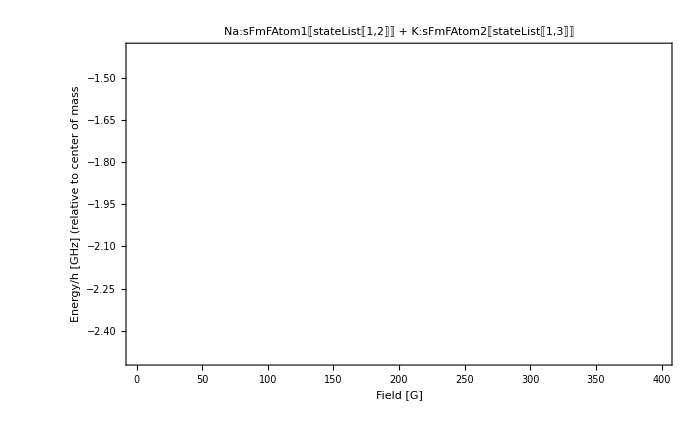

```mathematica
toPlot={1};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
qqP=getBS2[E0P,E1P,50000,50000,η0P,0.0,0.0,0.0,0];
qqD=getBS2[E0D,E1D,50000,50000,η0D,0.0,0.0,0.0,0];
Show[Plot[openChanFn[B],{B,0,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[qqP[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Blue]],
ListPlot[qqD[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Green]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]][[All,2]],PlotStyle->PointSize[0.015]],PlotRange->{-2.5,-1.4},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->700,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```

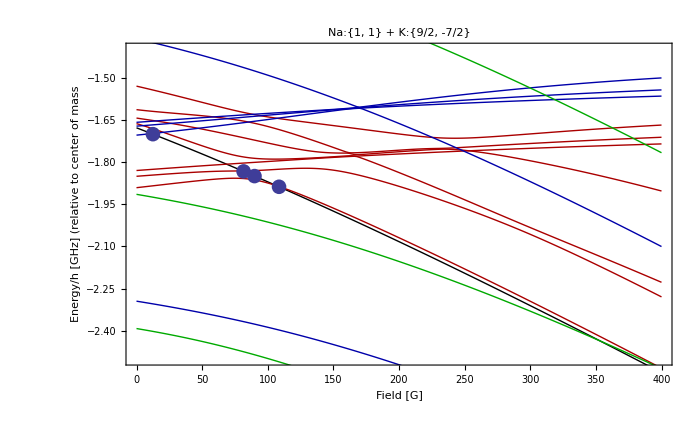

```mathematica
toPlot={2};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
qqP=getBS2[E0P,E1P,50000,50000,η0P,0.0,0.0,0.0,0];
qqD=getBS2[E0D,E1D,50000,50000,η0D,0.0,0.0,0.0,0];
Show[Plot[openChanFn[B],{B,0,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[qqP[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Blue]],
ListPlot[qqD[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Green]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]][[All,2]],PlotStyle->PointSize[0.015]],PlotRange->{-2.5,-1.4},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->700,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```

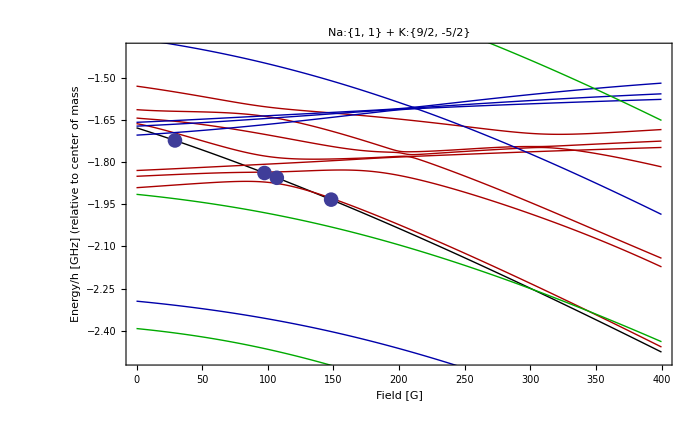

```mathematica
toPlot={3};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
qqP=getBS2[E0P,E1P,50000,50000,η0P,0.0,0.0,0.0,0];
qqD=getBS2[E0D,E1D,50000,50000,η0D,0.0,0.0,0.0,0];
Show[Plot[openChanFn[B],{B,0,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[qqP[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Blue]],
ListPlot[qqD[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Green]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]][[All,2]],PlotStyle->PointSize[0.015]],PlotRange->{-2.5,-1.4},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->700,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```

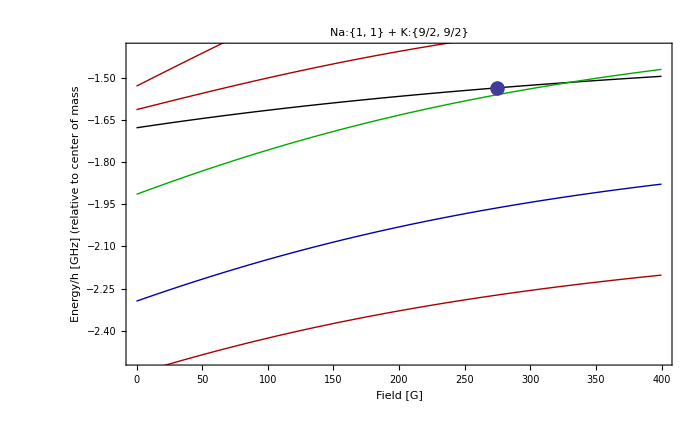

```mathematica
toPlot={10};
qqS=getBS2[E0S,E1S,E0S2,E1S2,η0S,η1S,η2S,η3S,0];
qqP=getBS2[E0P,E1P,50000,50000,η0P,0.0,0.0,0.0,0];
qqD=getBS2[E0D,E1D,50000,50000,η0D,0.0,0.0,0.0,0];
Show[Plot[openChanFn[B],{B,0,maxBPlot},PlotStyle->{{Thick,Black}}],
ListPlot[qqS[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Red]],
ListPlot[qqP[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Blue]],
ListPlot[qqD[[All,{1,1+#}]]&/@Range[Length[qqS[[1]]]-1],PlotRange->All,Joined->True,PlotStyle->Darker[Green]],
ListPlot[{#,openChanFn[#]}&/@Cases[MeasRes,x_/;x[[1]]==toPlot[[1]]][[All,2]],PlotStyle->PointSize[0.015]],PlotRange->{-2.5,-1.4},PlotLabel->"Na:"<>ToString[StandardForm@sFmFAtom1[[stateList[[iState,2]]]]]<>" + K:"<>ToString[StandardForm@sFmFAtom2[[stateList[[iState,3]]]]],Frame->True,Axes->None,ImageSize->700,FrameLabel->{"Field [G]","Energy/h [GHz] (relative to center of mass"},FrameStyle->18]
```